```mathematica
<<InfoHDP`
```

0.130812

{0.384095,0.130812}

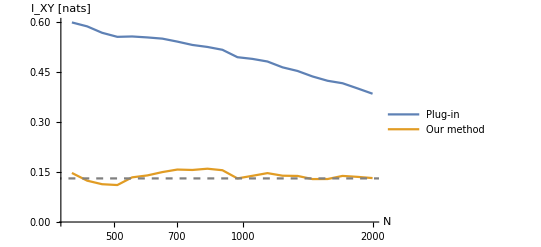

```mathematica
M=1000;(*number of x states*)
NN=2000;(*number of total samples*)
q1=0.75;
q1x=RandomChoice[{0.5,0.5}->{q1,(1.-q1)},M];(*conditional probabilities Pr(y=1|x) from two deltas*)
xs=RandomInteger[{1,M},NN];(*uniform probabilities in x*)
ys=Table[RandomChoice[{q1x[[xs[[i]]]],(1.-q1x[[xs[[i]]]])}->{1,-1}],{i,Length@xs}];
xys=xs*ys;(*Abs-> x, Sign-> y*)
Ixy=Log[2.]+q1 Log[q1]+(1.-q1)Log[1.-q1](*Expected information*)

(*Plug-in estimate and our method with NN samples(only beta as hyperparameter and no prior on beta)*)
{xys//Inaive,xys//IhdpMAP[#,1.,1.]&}

(*Let's plot the plug-in estimate and our method vs the number of samples*)
data=Table[Block[{nn=logn//Exp//Floor},
{nn,xys[[;;nn]]//Inaive,xys[[;;nn]]//IhdpMAP[#,1.,1.]&}],{logn,Log[400],Log[NN],Log[NN/400]/20.}];

plot={data[[All,{1,2}]],data[[All,{1,3}]]}//ListLogLinearPlot[#,
Joined->True,
AxesLabel->{"N","I_XY [nats]"},
PlotLegends->{"Plug-in","Our method"}]&;
Show[plot,Plot[Ixy,{m,0,2 NN},PlotStyle->{Dashed,Gray}]]
```